```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D-Sirius-22-10-aero\settings\airfoils

```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
(*Расширяющаяся труба - задача для внутреннего течения*)
(*pts={{6.3,0},{6.3,0.6},{-0.2,0.6},{-0.5,0.3},{-3.5,0.3},{-3.5,0},{-3.5,-0.3},{-0.5,-0.3},{-0.2,-0.6},{6.3,-0.6},{6.3,0}};
h=π/400.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента А.Н.Нуриева*)
(*pts={{0.05,0.0},{0.05,0.5},{-0.05,0.5},{-0.05,0.0},{-0.05,-0.5},{0.05,-0.5},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Профиль с заостренными концами - из эксперимента А.Н.Нуриева*)
(*H=√(0.1^2-0.05^2)
pts={{0.05,0.0},{0.05,0.5-H},{0.0,0.5},{-0.05,0.5-H},{-0.05,0.0},{-0.05,-0.5+H},{0.0,-0.5},{0.05,-0.5+H},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента В.А.Фролова*)
(*pts={{0.25,0.0},{0.25,0.025},{-0.25,0.025},{-0.25,0.0},{-0.25,-0.025},{0.25,-0.025},{0.25,0.0}};
h=π/100.;*)
```

```mathematica
(*Тонкая пластинка - для Моргенталя*)
(*pts={{16.5,0.0},{16.5,0.165},{-16.5,0.165},{-16.5,0.0},{-16.5,-0.165},{16.5,-0.165},{16.5,0.0}};
h=0.16/8.;*)
```

```mathematica
(*Профиль моста StructureA - для Моргенталя*)
(*pts={{16.5,0.0},{13.3,1.425},{-13.3,1.425},{-16.5,0.0},{-13.3,-1.425},{13.3,-1.425},{16.5,0.0}};
h=0.16/(2 8.);*)
```

```mathematica
(*Профиль моста StructureH - для Моргенталя*)
(*pts={{6.0,0.0},{6.0,1.2},{5.6,1.2},{5.6,0.2},{-5.6,0.2},{-5.6,1.2},{-6.0,1.2},{-6.0,0.0},{-6.0,-1.2},{-5.6,-1.2},{-5.6,-0.2},{5.6,-0.2},{5.6,-1.2},{6.0,-1.2},{6.0,0.0}};
h=0.06/8.;*)
```

```mathematica
(*Сапсан*)
```

```mathematica
pts={{127.36293,0.00000},{127.36384,0.14918},{127.35683,0.29820},{127.34849,0.37709},{127.33546,0.45535},{127.00295,0.99251},{126.40812,1.24854},{124.85860,1.46366},{123.29882,1.59231},{113.13441,1.59231},{102.97000,1.59231},{102.97000,1.16241},{102.97000,0.73250},{102.64000,0.73250},{102.31000,0.73250},{102.31000,1.16241},{102.31000,1.59231},{89.81000,1.59231},{77.31000,1.59231},{77.31000,1.16241},{77.31000,0.73250},{76.98000,0.73250},{76.65000,0.73250},{76.65000,1.16241},{76.65000,1.59231},{64.15000,1.59231},{51.65000,1.59231},{51.65000,1.16241},{51.65000,0.73250},{51.32000,0.73250},{50.99000,0.73250},{50.99000,1.16241},{50.99000,1.59231},{38.49000,1.59231},{25.99000,1.59231},{25.99000,1.16241},{25.99000,0.73250},{25.66000,0.73250},{25.33000,0.73250},{25.33000,1.16241},{25.33000,1.59231},{12.83000,1.59231},{0.33000,1.59231},{0.33000,1.16241},{0.33000,0.73250},{0.16500,0.73250},{0.00000,0.73250},{-0.16500,0.73250},{-0.33000,0.73250},{-0.33000,1.16241},{-0.33000,1.59231},{-12.83000,1.59231},{-25.33000,1.59231},{-25.33000,1.16241},{-25.33000,0.73250},{-25.66000,0.73250},{-25.99000,0.73250},{-25.99000,1.16241},{-25.99000,1.59231},{-38.49000,1.59231},{-50.99000,1.59231},{-50.99000,1.16241},{-50.99000,0.73250},{-51.32000,0.73250},{-51.65000,0.73250},{-51.65000,1.16241},{-51.65000,1.59231},{-64.15000,1.59231},{-76.65000,1.59231},{-76.65000,1.16241},{-76.65000,0.73250},{-76.98000,0.73250},{-77.31000,0.73250},{-77.31000,1.16241},{-77.31000,1.59231},{-89.81000,1.59231},{-102.31000,1.59231},{-102.31000,1.16241},{-102.31000,0.73250},{-102.64000,0.73250},{-102.97000,0.73250},{-102.97000,1.16241},{-102.97000,1.59231},{-113.13441,1.59231},{-123.29882,1.59231},{-124.85860,1.46366},{-126.40812,1.24854},{-127.00295,0.99251},{-127.33546,0.45535},{-127.34849,0.37709},{-127.35683,0.29820},{-127.36384,0.14918},{-127.36293,0.00000},{-127.36384,-0.14918},{-127.35683,-0.29820},{-127.34849,-0.37709},{-127.33546,-0.45535},{-127.00295,-0.99251},{-126.40812,-1.24854},{-124.85860,-1.46366},{-123.29882,-1.59231},{-113.13441,-1.59231},{-102.97000,-1.59231},{-102.97000,-1.16241},{-102.97000,-0.73250},{-102.64000,-0.73250},{-102.31000,-0.73250},{-102.31000,-1.16241},{-102.31000,-1.59231},{-89.81000,-1.59231},{-77.31000,-1.59231},{-77.31000,-1.16241},{-77.31000,-0.73250},{-76.98000,-0.73250},{-76.65000,-0.73250},{-76.65000,-1.16241},{-76.65000,-1.59231},{-64.15000,-1.59231},{-51.65000,-1.59231},{-51.65000,-1.16241},{-51.65000,-0.73250},{-51.32000,-0.73250},{-50.99000,-0.73250},{-50.99000,-1.16241},{-50.99000,-1.59231},{-38.49000,-1.59231},{-25.99000,-1.59231},{-25.99000,-1.16241},{-25.99000,-0.73250},{-25.66000,-0.73250},{-25.33000,-0.73250},{-25.33000,-1.16241},{-25.33000,-1.59231},{-12.83000,-1.59231},{-0.33000,-1.59231},{-0.33000,-1.16241},{-0.33000,-0.73250},{-0.16500,-0.73250},{0.00000,-0.73250},{0.16500,-0.73250},{0.33000,-0.73250},{0.33000,-1.16241},{0.33000,-1.59231},{12.83000,-1.59231},{25.33000,-1.59231},{25.33000,-1.16241},{25.33000,-0.73250},{25.66000,-0.73250},{25.99000,-0.73250},{25.99000,-1.16241},{25.99000,-1.59231},{38.49000,-1.59231},{50.99000,-1.59231},{50.99000,-1.16241},{50.99000,-0.73250},{51.32000,-0.73250},{51.65000,-0.73250},{51.65000,-1.16241},{51.65000,-1.59231},{64.15000,-1.59231},{76.65000,-1.59231},{76.65000,-1.16241},{76.65000,-0.73250},{76.98000,-0.73250},{77.31000,-0.73250},{77.31000,-1.16241},{77.31000,-1.59231},{89.81000,-1.59231},{102.31000,-1.59231},{102.31000,-1.16241},{102.31000,-0.73250},{102.64000,-0.73250},{102.97000,-0.73250},{102.97000,-1.16241},{102.97000,-1.59231},{113.13441,-1.59231},{123.29882,-1.59231},{124.85860,-1.46366},{126.40812,-1.24854},{127.00295,-0.99251},{127.33546,-0.45535},{127.34849,-0.37709},{127.35683,-0.29820},{127.36384,-0.14918},{127.36293,0.00000}};
h=0.20;
```

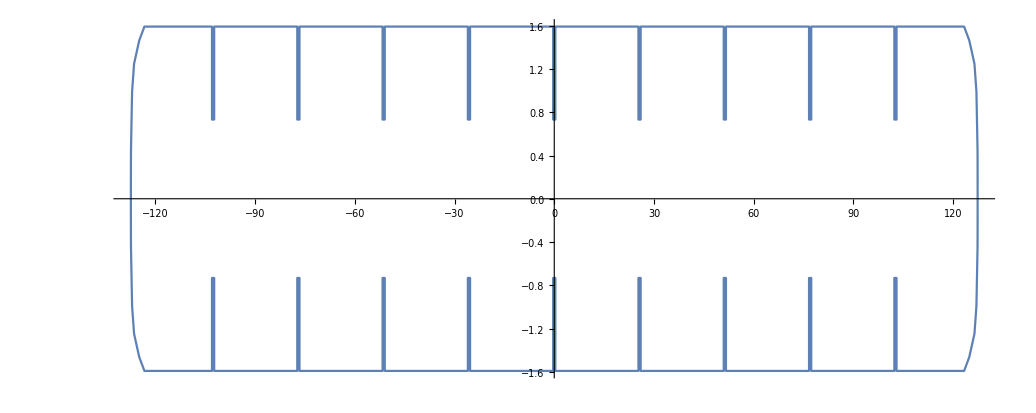

```mathematica
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
vertex=Flatten[Table[SplitLine[pts[[i]],pts[[i+1]],h,LastPoint->False],{i,Length@pts-1}],1];
```

```mathematica
n=Length@vertex
```

2824

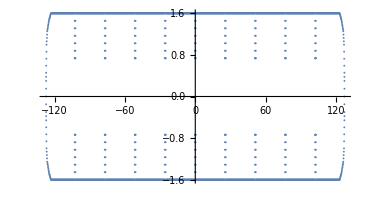

```mathematica
ListPlot[vertex,AspectRatio->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["sapsan2824",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: sapsan"<>StringRepeat[" ",49]<>"|
| Info: sapsan train ("<>TextString[n]<>" panels)"<>StringRepeat[" ",34-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/ 
"}~Join~{"r = {"}
~Join~
Table[{"{",TextString@vertex[[i,1]],",",TextString@vertex[[i,2]],"},"},{i,n-1}]
~Join~
{{"{",TextString@vertex[[-1,1]],",",TextString@vertex[[-1,2]],"}"}}
~Join~
{{"};"}}
,"Table"]
```

sapsan2824